With the Drude Lorentz spectral density

```mathematica
JDLnew[ω_,λ_,gamma_]:=(2 ω gamma λ)/(ω^2+gamma^2)
```

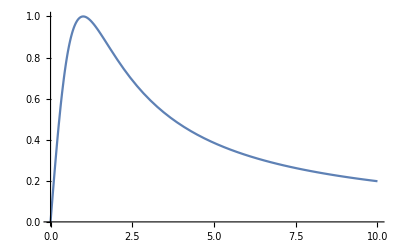

```mathematica
Plot[JDLnew[ω,1,1],{ω,0,10}]
```

Defining the real and imaginary part of the bath correlation fuction

```mathematica
νdirect[t_?NumericQ,β_?NumericQ,λ_?NumericQ,gamma_?NumericQ,Msup_?NumericQ]:=NIntegrate[JDLnew[ω,λ,gamma]/π Coth[(β ω)/2]Cos[ω t],{ω,0,Msup}]
ηdirect[t_?NumericQ,β_?NumericQ,λ_?NumericQ,gamma_?NumericQ,Msup_?NumericQ]:=NIntegrate[-JDLnew[ω,λ,gamma]/π Sin[ω t],{ω,0,Msup}]
(*last one not depending on beta*)
```

```mathematica
νdirect[1,1,1,1,Infinity]
ηdirect[1,1,1,1,Infinity]
```

0.67462

-0.367879

Defining the parameters used

```mathematica
Clear[γp,λp,Tp]
γp=1;
λp=0.2;
Tp=1;
```

Decay rate  on Markov and TCL2 (Born Redfield)

```mathematica
γMarkovDL[α_,β_,λ_,gamma_]:=2π JDLnew[α,λ,gamma]/π Coth[(β α)/2]
γTCL2indirect[t_,β_,λ_,gamma_,Msup_]:=2 NIntegrate[JDLnew[u,λ,gamma]/π Coth[(β u)/2] Sin[(u+1)t]/(u+1),{u,-Msup, Msup}]
```

```mathematica
γMarkovDL[1,1/Tp,λp,γp]
γTCL2indirect[1,1/Tp,λp,γp,100]
```

0.865581

0.946619

```mathematica
γMarkovPlusDL[α_,β_,λ_,gamma_]:=2 π JDLnew[α,λ,gamma]/π Exp[-β*α] 1/(1-Exp[-β*α]);
γPlusTCL2DL[t_,β_,λ_,gamma_,Msup_]:=2 NIntegrate[JDLnew[u,λ,gamma]/π 1/(1-Exp[-β*u])Sin[(u+1)t]/(u+1),{u,-Msup,Msup}]
```

```mathematica
γMarkovPlusDL[1,1/Tp,λp,γp]
γPlusTCL2DL[1,1/Tp,λp,γp,100]
```

0.232791

0.374964

Now let’s solv the differential equation

{{y→InterpolatingFunction[…]}}

NIntegrate::inumr: The integrand (0.127324 u Sin[(1+u) x])/((1-ⅇ^-u) (1+u) (1+u^2)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞,0.}}.

NIntegrate::inumr: The integrand (0.127324 u Coth[u/2] Sin[(1+u) x])/((1+u) (1+u^2)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {4.81037×10^7}. NIntegrate obtained 0.00233951 and 9.37684×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {4.81037×10^7}. NIntegrate obtained 0.00116965 and 5.41209×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {4.81037×10^7}. NIntegrate obtained 0.00233951 and 9.37684×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{{y→InterpolatingFunction[…]}}

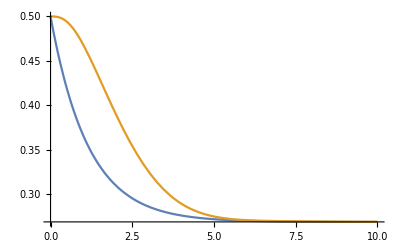

```mathematica
Clear[sMarkov,sTCL2]
sMarkov=NDSolve[{y'[x]==γMarkovPlusDL[1,1/Tp,λp,γp]-γMarkovDL[1,1/Tp,λp,γp]*y[x] ,y[0]==1/2},y,{x,0,10}]
sTCL2=NDSolve[{y'[x]==γPlusTCL2DL[x,1/Tp,λp,γp,Infinity]-γTCL2indirect[x,1/Tp,λp,γp,Infinity]*y[x] ,y[0]==1/2},y,{x,0,10}]
Plot[{Evaluate[y[x]/. sMarkov],Evaluate[y[x]/. sTCL2]},{x,0,10},PlotRange->All]
```

Now for TCL 4

```mathematica
Clear[γ4CompDirectai3,γ4CompDirectai2,γ4CompDirectai1]
```

```mathematica
γ4CompDirectai3[t_?NumericQ,t1_?NumericQ,t2_?NumericQ,β_?NumericQ,λ_?NumericQ,γ_?NumericQ,Msup_?NumericQ]:= -16NIntegrate[νdirect[t-t2,β,λ,γ,Msup]*νdirect[t1-t3,β,λ,γ,Msup]Sin[t-t3]Sin[t1-t2]+νdirect[t-t3,β,λ,γ,Msup]*νdirect[t1-t2,β,λ,γ,Msup]Sin[t-t2]Sin[t1-t3],{t3,0,t2}]
γ4CompDirectai2[t_?NumericQ,t1_?NumericQ,β_?NumericQ,λ_?NumericQ,γ_?NumericQ,Msup_?NumericQ]:= NIntegrate[γ4CompDirectai3[t,t1,t2,β,λ,γ,Msup],{t2,0,t1}]
γ4CompDirectai1[t_?NumericQ,β_?NumericQ,λ_?NumericQ,γ_?NumericQ,Msup_?NumericQ]:= NIntegrate[γ4CompDirectai2[t,t1,β,λ,γ,Msup],{t1,0,t}]
Timing[γ4CompDirectai2[2,12,1/Tp,λp,γp,1]]
```

{249.553,-0.257204}

```mathematica
gα1[t_,t1_,t2_,β_,λ_,γ_,Msup_]:=NIntegrate[JDLnew[u,λ,γ]/π Coth[(β u)/2](Sin[1/2 t2 (u+1)] Sin[t +u*t1-1/2 t2 (1+u)])/(1+u),{u,-Msup,Msup}]
gα2[t_,t1_,t2_,β_,λ_,γ_,Msup_]:=NIntegrate[JDLnew[u,λ,γ]/π Coth[(β u)/2](Sin[1/2 t2 (u+1)] Sin[t1 +u*t-1/2 t2 (1+u)])/(1+u),{u,-Msup,Msup}]
γ4CompIndirectai2[t_?NumericQ,t1_?NumericQ,β_?NumericQ,λ_?NumericQ,γ_?NumericQ,Msup_?NumericQ]:= -16NIntegrate[νdirect[t-t2,β,λ,γ,Msup]*Sin[t1-t2]gα1[t,t1,t2,β,λ,γ,Msup]+νdirect[t1-t2,β,λ,γ,Msup]*Sin[t-t2]gα2[t,t1,t2,β,λ,γ,Msup],{t2,0,t1}]

Timing[γ4CompIndirectai2[1,1,1/Tp,λp,γp,1]]
```

NIntegrate::inumr: The integrand (0.127324 ω Cos[(1-t2) ω] Coth[ω/2])/(1+ω^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

NIntegrate::inumr: The integrand (0.127324 u Coth[u/2] Sin[1/2 t2 (1+u)] Sin[1+u-1/2 t2 (1+u)])/((1+u) (1+u^2)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-1,1}}.

NIntegrate::inumr: The integrand (0.127324 ω Cos[(1-t2) ω] Coth[ω/2])/(1+ω^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{5.10191,-0.12342}

```mathematica
Timing[γ4CompIndirectai2[1,1,1/Tp,λp,γp,100]]
```

NIntegrate::inumr: The integrand (0.127324 ω Cos[(1-t2) ω] Coth[ω/2])/(1+ω^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,100}}.

NIntegrate::inumr: The integrand (0.127324 u Coth[u/2] Sin[1/2 t2 (1+u)] Sin[1+u-1/2 t2 (1+u)])/((1+u) (1+u^2)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-100,100}}.

NIntegrate::inumr: The integrand (0.127324 ω Cos[(1-t2) ω] Coth[ω/2])/(1+ω^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,100}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{16.2571,-0.140899}

```mathematica
γ4Indirecta[t_?NumericQ,β_?NumericQ,λ_?NumericQ,γ_?NumericQ,Msup_?NumericQ]:= NIntegrate[γ4CompIndirectai2[t,t1,β,λ,γ,Msup],{t1,0,t}]
```

Now for tcl plus 4 WE HAVE

γ4+=8∫_0^t ∫_0^t1 ∫^t2 [-η03 ν12 s23 c01+(η12 ν03+ η13  ν02) s12  c03]+γ4/2
For the first integral
∫_0^t ∫_0^t1 ∫^t2 -η03 ν12 s23 c01=-   ∫_0^t c01∫_0^t1 ν12∫^t2 η03  s23

```mathematica
FullSimplify[Integrate[Cos[t-t1]Integrate[Cos[v(t1-t2)]Integrate[Sin[u(t-t3)]*Sin[t2-t3],{t3,0,t2}],{t2,0,t1}],{t1,0,t}]]
```

-((2 (-1+u^2)^2 v^2 Cos[t v] Sin[t u]+(u-v) (u+v) Sin[t] (u (-3+u^2+(1+u^2) v^2) Cos[t u]+t (-1+u^2) (-1+v^2) Sin[t u])+(u-v) (u+v) Cos[t] (t u (-1+u^2) (-1+v^2) Cos[t u]-2 (-1+u^2 v^2) Sin[t u])-2 u (-1+u^2)^2 v Cos[t u] Sin[t v])/(2 (-1+u^2)^2 (u-v) (u+v) (-1+v^2)^2))

```mathematica
gβ1[t_?NumericQ,t1_?NumericQ,t2_?NumericQ,β_?NumericQ,λ_?NumericQ,γ_?NumericQ,Msup_?NumericQ]:=NIntegrate[-JDLnew[u,λ,γ]/π(1/(1-u^2)(u Cos[t u]Sin[t2]-Cos[t2]Sin[t u]+Sin[(t-t2)u])),{u,0,Msup}]
gβ1[1,1,1,1/Tp,λp,γp,10]
```

-0.0496196

```mathematica
β1IndirSinIntegrar[t_?NumericQ,t1_?NumericQ,β_?NumericQ,λ_?NumericQ,γ_?NumericQ,Msup_?NumericQ]:=(-Cos[t-t1])NIntegrate[νdirect[t1-t2,β,λ,γ,Msup]*gβ1[t,t1,t2,β,λ,γ,Msup],{t2,0,t1}]
β1IndirSinIntegrar[10,10,1/Tp,λp,γp,400]
```

NIntegrate::inumr: The integrand (0.127324 ω Cos[(10-t2) ω] Coth[ω/2])/(1+ω^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,400}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t2 near {t2} = {9.65710190852880823175752311726682819426059722900390625}. NIntegrate obtained -0.0213492 and 2.70512×10^-8 for the integral and error estimates.

0.0213492

β4+=∫_0^t ∫_0^t1 ∫^t2 [(η12 ν03) s12  c03]=∫_0^t ∫_0^t1 η12 s12∫^t2 ν03  c03

```mathematica
FullSimplify[Integrate[Cos[u(t-t3)]*Cos[1(t-t3)],{t3,0,t2}]]
```

1/(2 (-1+u^2))((1+u) Sin[t (-1+u)]+(1+u) Sin[(-t+t2) (-1+u)]+(-1+u) (Sin[t (1+u)]-Sin[(t-t2) (1+u)]))

```mathematica
gβ4[t_?NumericQ,t1_?NumericQ,t2_?NumericQ,β_?NumericQ,λ_?NumericQ,γ_?NumericQ,Msup_?NumericQ]:=NIntegrate[JDLnew[u,λ,γ]/π Coth[(β u)/2](1/(2 (-1+u^2))((1+u) Sin[t (-1+u)]+(1+u) Sin[(-t+t2) (-1+u)]+(-1+u) (Sin[t (1+u)]-Sin[(t-t2) (1+u)]))),{u,0,Msup}]
(*β4Indirecti2[t_?NumericQ,t1_?NumericQ,β_?NumericQ,λ_?NumericQ,γ_?NumericQ,Msup_?NumericQ]:=NIntegrate[JDLnew[u,λ,γ]/π Coth[(β u)/2]((Sin[t(u+1)]-Sin[(t-t2)*(u+1)])/(2(1+u))),{u,-Msup,Msup}]*)
β4IndirSinIntegrar[t_?NumericQ,t1_?NumericQ,β_?NumericQ,λ_?NumericQ,γ_?NumericQ,Msup_?NumericQ]:=NIntegrate[ηdirect[t1-t2,β,λ,γ,Msup]*Sin[t1-t2]*gβ4[t,t1,t2,β,λ,γ,Msup],{t2,0,t1}]
β4IndirSinIntegrar[1,2,1/Tp,λp,γp,100]
```

NIntegrate::inumr: The integrand -(0.127324 ω Sin[(2-t2) ω])/(1+ω^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,100}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

-0.0226605

β5=∫_0^t ∫_0^t1 ∫^t2 η13  ν02 s12  c03=∫_0^t ∫_0^t1 ν02 s12 ∫^t2 η13   c03

```mathematica
Integrate[Sin[u(t1-t3)]Cos[t-t3],{t3,0,t2}]
```

-(Sin[1/2 t2 (-1+u)] Sin[t+1/2 t2 (-1+u)-t1 u])/(-1+u)+(Sin[1/2 t2 (1+u)] Sin[t+t1 u-1/2 t2 (1+u)])/(1+u)

```mathematica
(*gβ5[t_?NumericQ,t1_?NumericQ,t2_?NumericQ,β_?NumericQ,λ_?NumericQ,γ_?NumericQ,Msup_?NumericQ]:=NIntegrate[-JDLnew[u,λ,γ]/π((Sin[1/2 t2(u+1)]*Sin[t+u t1-1/2 t2(u+1)])/(1+u)),{u,-Msup,Msup}]*)
gβ5[t_?NumericQ,t1_?NumericQ,t2_?NumericQ,β_?NumericQ,λ_?NumericQ,γ_?NumericQ,Msup_?NumericQ]:=NIntegrate[-JDLnew[u,λ,γ]/π(-(Sin[1/2 t2 (-1+u)] Sin[t+1/2 t2 (-1+u)-t1 u])/(-1+u)+(Sin[1/2 t2 (1+u)] Sin[t+t1 u-1/2 t2 (1+u)])/(1+u)),{u,0,Msup}]
β5IndirSinIntegrar[t_?NumericQ,t1_?NumericQ,β_?NumericQ,λ_?NumericQ,γ_?NumericQ,Msup_?NumericQ]:=NIntegrate[νdirect[t-t2,β,λ,γ,Msup]*Sin[t1-t2]*gβ5[t,t1,t2,β,λ,γ,Msup],{t2,0,t1}]

Timing[β5IndirSinIntegrar[20,1,1/Tp,λp,γp,100]]
```

NIntegrate::inumr: The integrand (0.127324 ω Cos[(20-t2) ω] Coth[ω/2])/(1+ω^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,100}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{49.4253,8.2956×10^-10}

```mathematica
γ4PlusIndirectai2[t_,t1_,β_,λ_,γ_,Msup_]:=8*(β1IndirSinIntegrar[t,t1,β,λ,γ,Msup]+β4IndirSinIntegrar[t,t1,β,λ,γ,Msup]+β5IndirSinIntegrar[t,t1,β,λ,γ,Msup])+γ4CompIndirectai2[t,t1,β,λ,γ,Msup]/2

γ4PlusIndirectai2[1,2,1/Tp,λp,γp,10]
```

NIntegrate::inumr: The integrand (0.127324 ω Cos[(2-t2) ω] Coth[ω/2])/(1+ω^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,10}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

0.155314

```mathematica
γ4PlusIndirectai1[t_?NumericQ,β_?NumericQ,λ_?NumericQ,γ_?NumericQ,Msup_?NumericQ]:= NIntegrate[γ4PlusIndirectai2[t,t1,β,λ,γ,Msup],{t1,0,t}]
```

```mathematica
γ4PlusDirectai3[t_?NumericQ,t1_?NumericQ,t2_?NumericQ,β_?NumericQ,λ_?NumericQ,γ_?NumericQ,Msup_?NumericQ]:= 8NIntegrate[-ηdirect[t-t3,β,λ,γ,Msup]*νdirect[t1-t2,β,λ,γ,Msup]Sin[t2-t3]Cos[t-t1]-νdirect[t-t3,β,λ,γ,Msup]*νdirect[t1-t2,β,λ,γ,Msup]Sin[t-t2]Sin[t1-t3]-νdirect[t-t2,β,λ,γ,Msup]*νdirect[t1-t3,β,λ,γ,Msup]Sin[t-t3]Sin[t1-t2]+(ηdirect[t1-t2,β,λ,γ,Msup]*νdirect[t-t3,β,λ,γ,Msup]+ηdirect[t1-t3,β,λ,γ,Msup]*νdirect[t-t2,β,λ,γ,Msup])*Sin[t1-t2]Cos[t-t3],{t3,0,t2}]
γ4PlusDirectai2[t_?NumericQ,t1_?NumericQ,β_?NumericQ,λ_?NumericQ,γ_?NumericQ,Msup_?NumericQ]:= NIntegrate[γ4PlusDirectai3[t,t1,t2,β,λ,γ,Msup],{t2,0,t1}]
γ4PlusDirectai1[t_?NumericQ,β_?NumericQ,λ_?NumericQ,γ_?NumericQ,Msup_?NumericQ]:= NIntegrate[γ4PlusDirectai2[t,t1,β,λ,γ,Msup],{t1,0,t}]
(*Timing[γ4PlusDirectai2[2,12,1/Tp,λp,γp,1]]*)
```

```mathematica
Timing[γ4PlusIndirectai2[2,12,1/Tp,λp,γp,10]]
```

NIntegrate::inumr: The integrand (0.127324 ω Cos[(12-t2) ω] Coth[ω/2])/(1+ω^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,10}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{140.746,-0.0874179}

```mathematica
Timing[γ4PlusIndirectai1[2,1/Tp,λp,γp,1]]
```

{155.111,-0.252906}

$Aborted

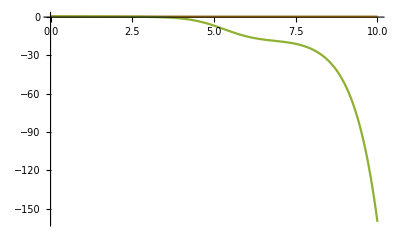

```mathematica
sTCL4=NDSolve[{y'[x]==γ4PlusIndirectai1[x,1/Tp,λp,γp,10]-γ4Indirecta[x,1/Tp,λp,γp,10]*y[x] ,y[0]==1/2},y,{x,0,10}]
Plot[{Evaluate[y[x]/. sMarkov],Evaluate[y[x]/. sTCL2],Evaluate[y[x]/. sTCL4]},{x,0,10},PlotRange->All]
```

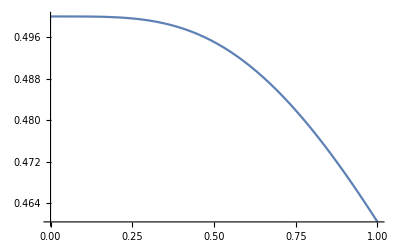

```mathematica
Plot[Evaluate[y[x]/. sTCL4],{x,0,1},PlotRange->All]
```